```mathematica
Clear["Global`*"]
```

# Check Data

## Check Long’s data that it satisfies the ODE January 2022

```mathematica
data = Import["/Users/cory/Sync/USYD/Denison/MATLAB/PQS analytic/PureQuartic.csv"];
```

```mathematica
DataDerivative[l_, n_]:=With[{pad=10},ArrayPad[DerivativeFilter[ArrayPad[l,pad,"Extrapolated"],{n}],-pad]];
```

```mathematica
d4 = DataDerivative[data[[;;,2]], 4];
```

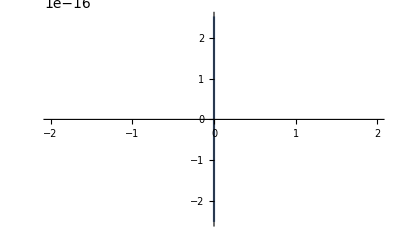

```mathematica
ListLinePlot[Transpose[{data[[;;,1]], DataDerivative[data[[;;,2]], 1]}], PlotRange->{{-2,2},Automatic}]
```